PMR Forces in 2D (x_,z_)

Basic Formulas and Definitions:

(F⃗)_mag=μ_0((m⃗)_eff·OverVector[∇])H⃗
H⃗=H_x(x,z)x^⋀+H_z(x,z)z^⋀

Fields calculated from Lytvinov and Kryder

H_x=(-8 M_r)/π^2∑_n [1/n cos(nπx/a)(1-e^(-nπδ/a))e^(-nπz/a)]
H_z=(-8 M_r)/π^2∑_n [1/n sin(nπx/a)(1-e^(-nπδ/a))e^(-nπz/a)]
(F⃗)_mag=F_(mag,x)(x,z)x^⋀+F_(mag,z)(x,z)z^⋀ 


genaral formulation of effective dipole moment method (Furlani) 

F_(mag,x)(x,z)=μ_0 V_p f(H)[H_x(x,z)(∂H_x(x,z))/(∂x)+H_z(x,z)(∂H_x(x,z))/(∂z)]
F_(mag,z)(x,z)=μ_0 V_p f(H)[H_x(x,z)(∂H_z(x,z))/(∂x)+H_z(x,z)(∂H_z(x,z))/(∂z)]

(F⃗)_mag=μ_0 V_P((M⃗)_eff·OverVector[∇])H⃗

In general 

f(H)=Piecewise[{{(3(χ_p-χ_f))/((χ_p-χ_f)+3), H<(((χ_p-χ_f)+3)/(3 χ_p))M_p}, {M_p/H, H≥(((χ_p-χ_f)+3)/(3 χ_p))M_p}}]   (|χ_f|≪1)    ,   H=|H⃗|    

χ_(f =μ_p/(μ_0-1))      susceptibility of the fluild 

The intrinsic magnetic susceptibility of the particle, i.e.   M_p=χ_p H_in where  H_in field inside the particle different from H by demagnetizing field H_in=H-N_d M_p and for spherical particle N_d=1/3. The value of  χ_p   can be obtaind from measured M v H cureve (hysteresis) but ofter M is plotted as a function of H in which case M_p=χ_a H where χ_ais apparent susceptibility. The two values of susceptibility are related as χ_p=χ_a/(1-N_d χ_a) reduces to χ_p=(3 χ_a)/(3-χ_a)

let for a spherical particle     H_Demag=M_p/3 
f(H)=Piecewise[{{3, H<M_p/3}, {M_p/H, otherwise}}]

a = period spacing in nanometers [nm]
M_r = remanent magnetization in amperes/meter  [A]/[m]
δ = height above the media in nanometers [nm]
μ_p= permeability for a particle
μ_0= permiability of free space 
V_p= volume of a particle in namometers cubed [(nm])^3, 	V_p=4/3 πr^3
r = particle radius [nm]
ρ = particle density [g]/[cm]^3or [g]/[10^7 nm]^3
H_z: Field in z direction 
H_x: Field in x direction
HgZZ: z component of Hz Field Gradient  
HgZX: x component of Hz Field Gradient  
HgXZ: z component of Hx Field Gradient  
HgXX: x component of Hz Field Gradient

```mathematica
(*r=200nm* pattent case)
```

```mathematica
Mr=6.5 10^5;
μ0=4 Pi 10^-7;
ρ =5.175;
```

```mathematica
Vp[r_]=4/3 π r^3;
```

```mathematica
fH[H_,Mp_,]:=If[H<Mp/3,3,Mp/H];
```

```mathematica
Hx[x_,z_]:=(-(8Mr)/π^2 )Sum[1/n Cos[(n π x)/a](1-Exp[-(n π δ)/a])Exp[-(n π z)/a],{n,1,50,2}]
Hz[x_,z_]:=((8Mr)/π^2 )Sum[1/n Sin[(n π x)/a](1-Exp[-(n π δ)/a])Exp[-(n π z)/a],{n,1,50,2}]
```

```mathematica
HgXX[x_,z_]:=Evaluate[D[Hx[x,z],x]];
HgXZ[x_,z_]:=Evaluate[D[Hx[x,z],z]];
HgZX[x_,z_]:=Evaluate[D[Hz[x,z],x]];
HgZZ[x_,z_]:=Evaluate[D[Hz[x,z],z]];
```

```mathematica
FmagX[x_,z_,r_,Mp_]:=μ0 Vp[r]fH[Sqrt[Hx[x,z]^2+Hz[x,z]^2],Mp]( Hx[x,z]HgXX[x,z]+Hz[x,z]HgXZ)
FmagZ[x_,z_,r_,Mp_]:=μ0 Vp[r]fH[Sqrt[Hx[x,z]^2+Hz[x,z]^2],Mp]( Hx[x,z]HgZX[x,z]+Hz[x,z]HgZZ)
```

```mathematica
Manipulate[Plot[μ0 Hz[x,z], {z,1,100}, PlotRange->{{x1,y1},{x2,y2}},Frame->True],{x,0,20},{a,1,1500},{δ,1,50},{x1,-100,100},{y1,-1,1},{x2,-100,100},{y2,-100,100}]
```

```mathematica
Manipulate[Plot[μ0 Hz[x,z], {z,1,100}, PlotRange->{{x1,y1},{x2,y2}},Frame->True],{x,0,20},{a,1,1500},{δ,1,50},{x1,-100,100},{y1,-1,1},{x2,-1,1},{y2,-100,100}]
```

```mathematica
a=1500
```

1500

```mathematica
δ=50
```

50

```mathematica
x=10
```

10

```mathematica
Clear[a,x,δ]
```

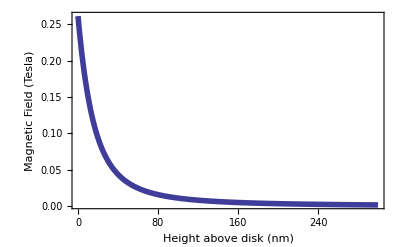

```mathematica
Plot[ μ0 Hz[10,z],{z,0,300},PlotRange->All,Frame->True,FrameLabel->{"Height above disk (nm)","Magnetic Field (Tesla)"},PlotStyle->{{Thickness->0.01}},GridLines->None,FrameStyle->{{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]},{Directive[Thick,FontFamily->"Arial",Black,18],Directive[Thick,FontFamily->"Arial",Black,18]}}]
```

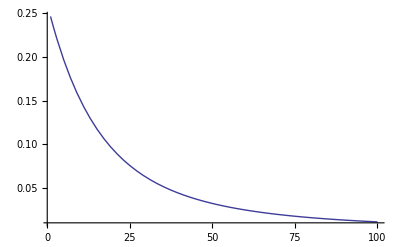

```mathematica
Plot[ μ0((8Mr)/π^2 )Sum[1/n Sin[(n π x)/a](1-Exp[-(n π δ)/a])Exp[-(n π z)/a],{n,1,50,2}],{z,1,100},PlotRange->All]
```

```mathematica
Plot[((8Mr)/π^2 )Sum[1/n Sin[(n π z)/a](1-Exp[-(n π δ)/a])Exp[-(n π z)/a],{n,1,50,2}]
```

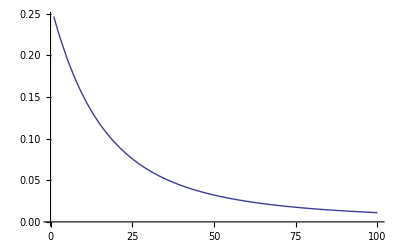

```mathematica
Plot[μ0((8Mr)/π^2 )Sum[1/n Sin[(n π 10)/1500](1-Exp[-(n π 50)/1500])Exp[-(n π z)/1500],{n,1,50,2}],{z,1,100},PlotRange->Automatic]
```

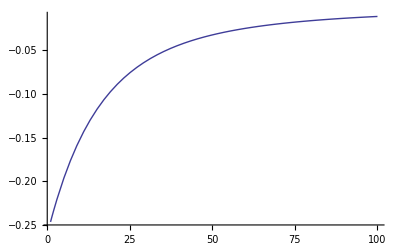

```mathematica
Plot[μ0(-(8Mr)/π^2 )Sum[1/n Sin[(n π 10)/1500](1-Exp[-(n π 50)/1500])Exp[-(n π z)/1500],{n,1,50,2}],{z,1,100},PlotRange->All]
```

```mathematica
Plot[μ0((-8*6.5 10^5)/π^2 )*Sum[((1/n)*Sin[(n*Pi*10)/1500]*(1-Exp[-Pi*(n/1500)*50])*Exp[-Pi*(n/1500)*z]),{n,1,50,2}],{z,1,100}, PlotRange->All]
```

-Graphics-

```mathematica
Plot[μ0((8*6.5 10^5)/π^2 )*Sum[((1/n)*Sin[(n*Pi*10)/1500]*(1-Exp[-Pi*(n/1500)*50])*Exp[-Pi*(n/1500)*z]),{n,1,50,2}],{z,1,100}, PlotRange->All]
```

-Graphics-

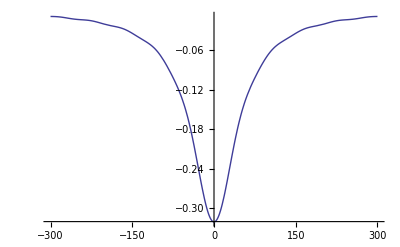

```mathematica
Plot[μ0((-8*6.5 10^5)/π^2 )*Sum[((1/n)*Cos[(n*Pi*x)/1500]*(1-Exp[-Pi*(n/1500)*50])*Exp[-Pi*(n/1500)*30]),{n,1,50,2}],{x,-300,300}, PlotRange->All]
```

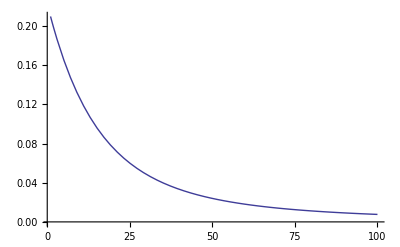

```mathematica
Plot[μ0((8 mr)/π^2 )*Sum[((1/n)*Sin[(n*Pi*10)/a]*(1-Exp[-Pi*(n/a)*δ])*Exp[-Pi*(n/a)*z]),{n,1,50,2}],{z,1,100}]
```